## Kay just asked me to check the convergence of SOR

```mathematica
FS=FullSimplify;
```

# Comparison with reference (i.e. convergence with high precision) Size: L=141

## tol - 0.100000

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

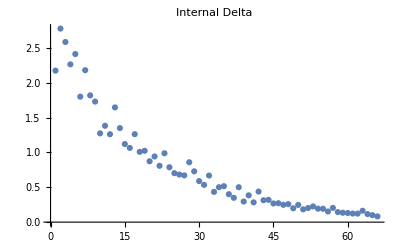
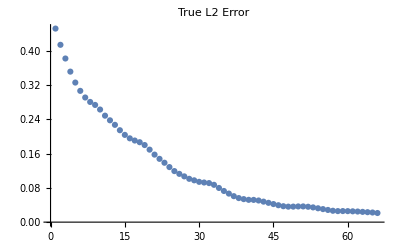
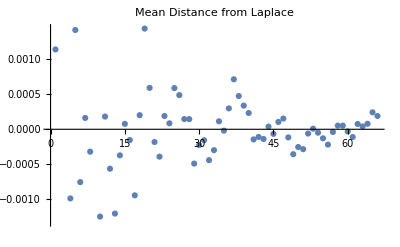

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-tol-0.100000.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],ImageSize->{400,300}],{i,2,numCols}]]
```

## tol - 0.010000

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

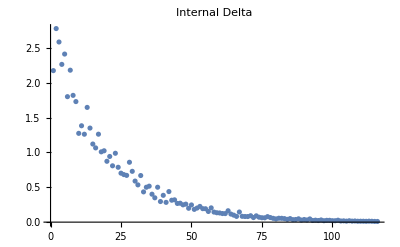
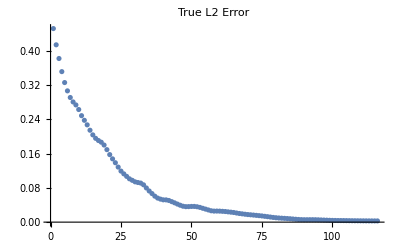
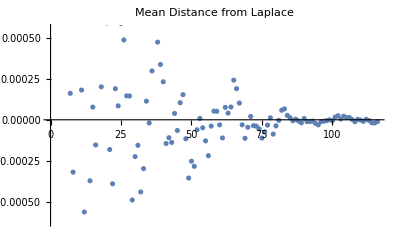

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.010000.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],ImageSize->{400,300}],{i,2,numCols}]]
```

## tol - 0.001000 Good-ish from here

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

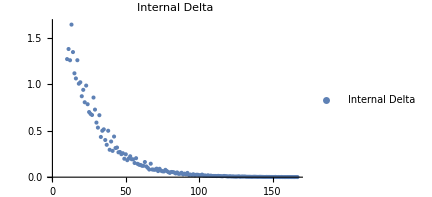
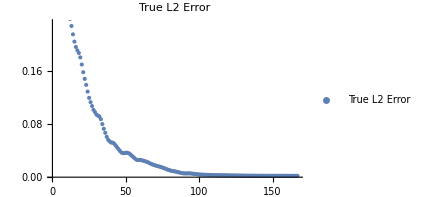
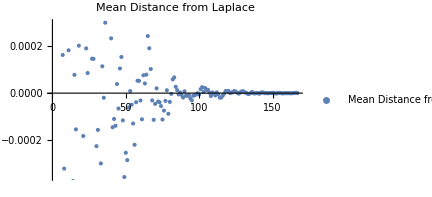

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.001000.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[plots001000=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

## tol - 0.000100

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

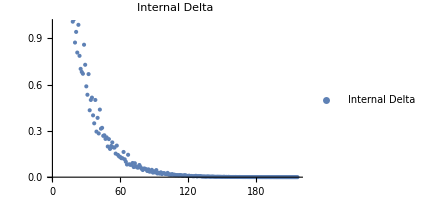
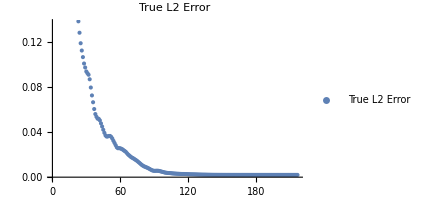
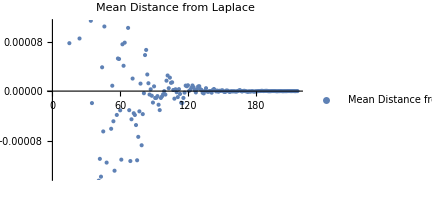

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.000100.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[plots000100=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

## tol - 0.000010

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

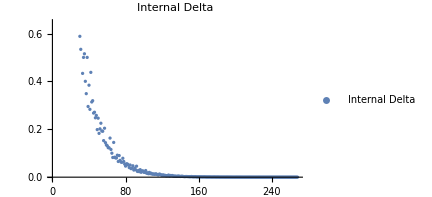
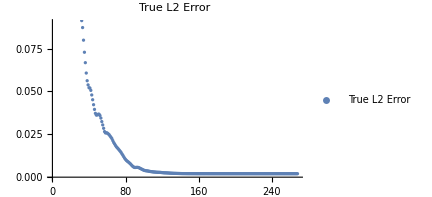
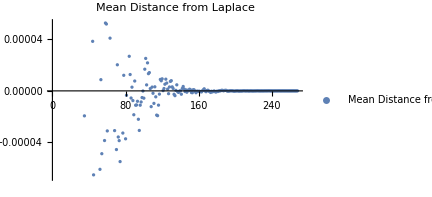

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.000010.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[plots000010=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

## tol - 0.000001

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

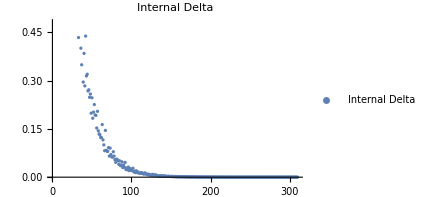
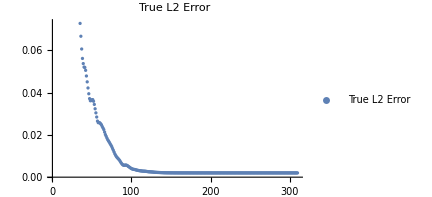
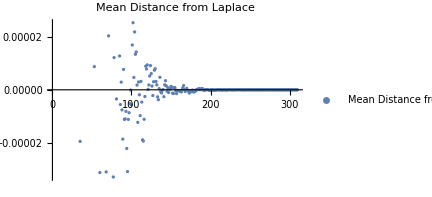

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.000001.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[plots000001=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

## tol - 0.000000(1) (in the file name it is not readable)

{Iteration #1,Delta Internal,Error L2 True,Distance from Laplace Mean}

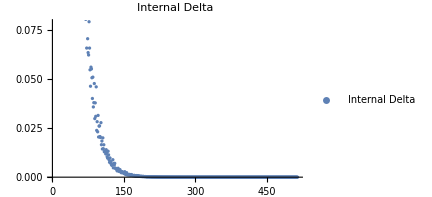
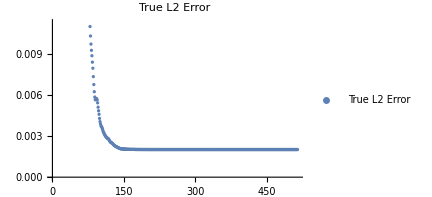
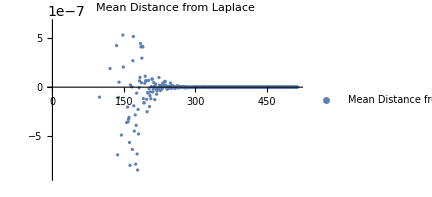

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\2dLaplaceEqSolution-conv-tol-0.000000.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","True L2 Error","Mean Distance from Laplace"};

Row[plots000000=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

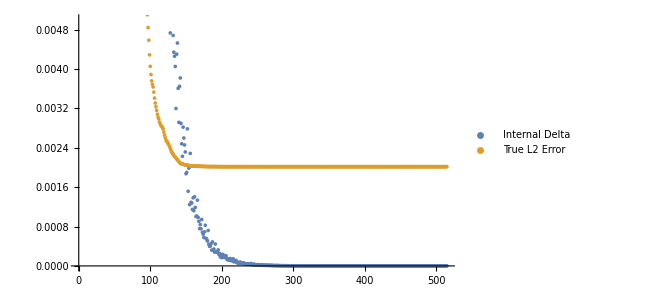

```mathematica
ListPlot[Table[
rawData[[All,{1,i}]],{i,2,3}],
PlotLegends->lables[[{1,2}]],ImageSize->1.2*{400,300},PlotRange->{All,{0,0.005}}
]
```

## tol - e - 10

{Iteration #1,Delta Internal,Distance from Laplace Mean,Error L2 True,Absolute Error Mean}

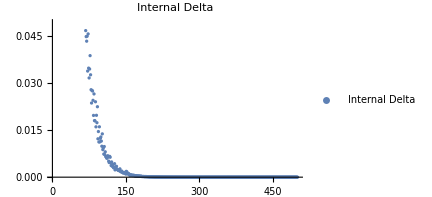
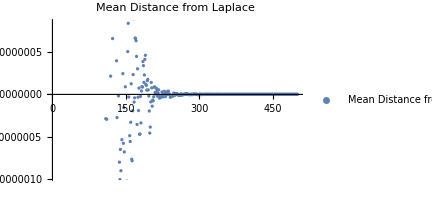
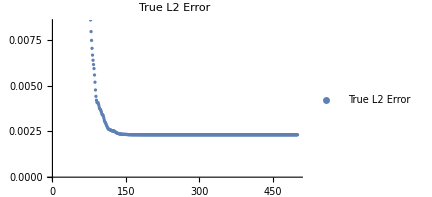
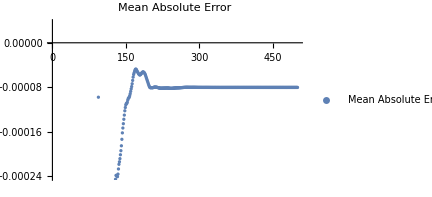

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size141-tol-e-10.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace","True L2 Error","Mean Absolute Error"};

Row[plotsm10=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

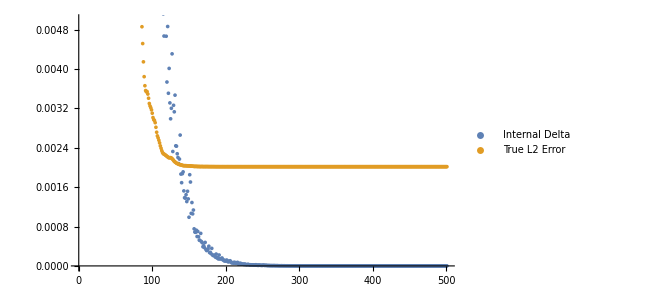

```mathematica
ListPlot[{
rawData[[All,{1,2}]],rawData[[All,{1,4}]]},
PlotLegends->lables[[{1,3}]],ImageSize->1.2*{400,300},PlotRange->{All,{0,0.005}}
]
```

## 2dLaplaceEqSolution-ConvComp-size141-tol-e-10

{Iteration #1,Delta Internal,Distance from Laplace Mean,Error Mean,Absolute Error Mean,Error Mean Square}

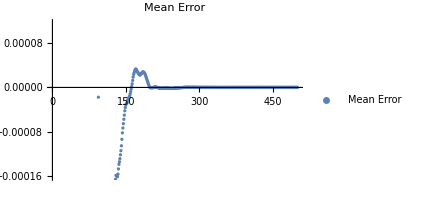
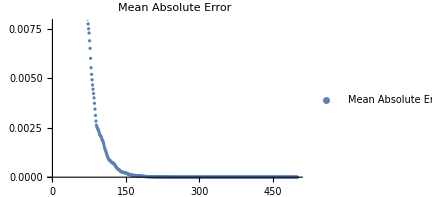
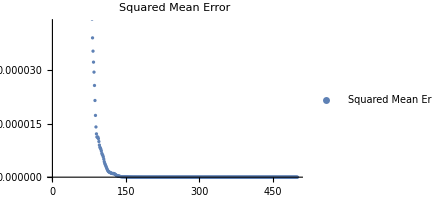
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-ConvComp-size141-tol-e-10.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace","Mean Error","Mean Absolute Error","Squared Mean Error"};

Row[plotsm10=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

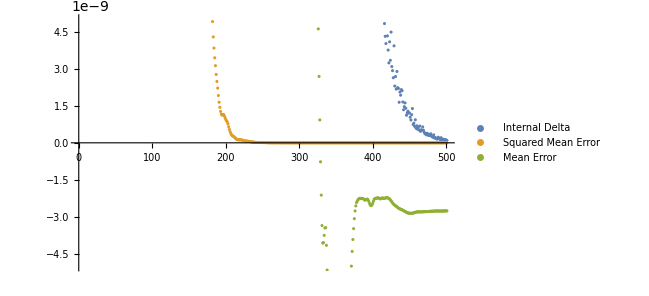

```mathematica
compareWith=6;
andWith=4;

yRange=0.000000005;

ListPlot[{
rawData[[All,{1,2}]]
,rawData[[All,{1,compareWith}]]
,rawData[[All,{1,andWith}]]
},
PlotLegends->lables[[{1,compareWith-1,andWith-1}]],ImageSize->1.2*{400,300},PlotRange->{All,{-yRange,yRange}}
]
```

## 2dLaplaceEqSolution-ConvComp-size141-tol-e-12

{Iteration #1,Delta Internal,Distance from Laplace Mean,Error Mean,Absolute Error Mean,Error Mean Square,Error Mean Sqrt Square,Distance From Mean Reference Relative}

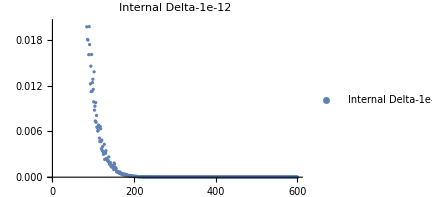
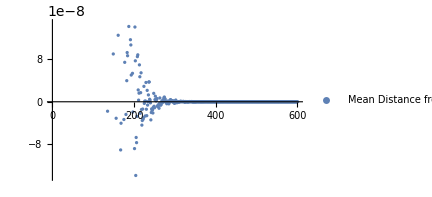
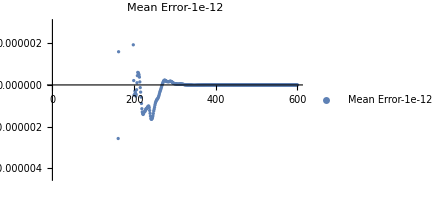
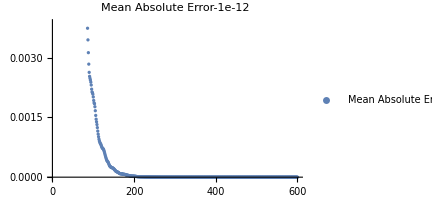
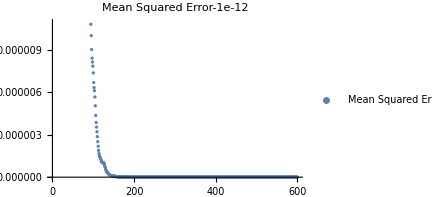
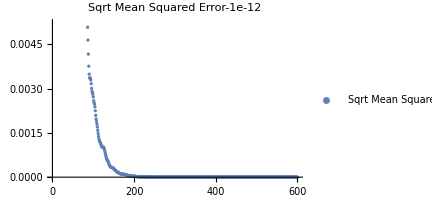
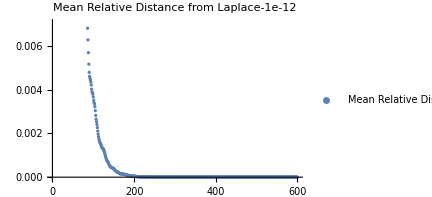

```mathematica
L=141;

rawData12=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-ConvComp-size141-tol-e-12.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData12[[1]]
rawData12 = Delete[rawData12,1];

numCols=Last[Dimensions[rawData12]];
lables12={"Internal Delta-1e-12","Mean Distance from Laplace-1e-12","Mean Error-1e-12","Mean Absolute Error-1e-12","Mean Squared Error-1e-12","Sqrt Mean Squared Error-1e-12","Mean Relative Distance from Laplace-1e-12"};

Row[plotsm10=Table[
ListPlot[rawData12[[All,{1,i}]],
PlotLabel->lables12[[i-1]],PlotLegends->Placed[{lables12[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

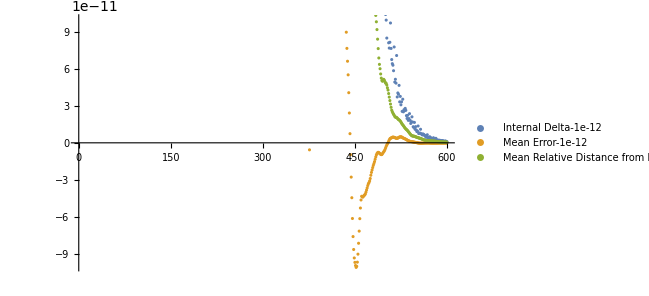

```mathematica
compareWith=4;
andWith=8;

yRange=10^(-10);

ListPlot[{rawData12[[All,{1,2}]]
,rawData12[[All,{1,compareWith}]]
,rawData12[[All,{1,andWith}]]
},
PlotLegends->lables12[[{1,compareWith-1,andWith-1}]],ImageSize->1.2*{400,300},PlotRange->{All,{-yRange,yRange}}
]
```

## 2dLaplaceEqSolution-ConvComp-WithRelativeError-size141-tol-e-15.dat

{Iteration #1,Delta Internal,Error Relative,Distance from Laplace Mean,Error Mean,Absolute Error Mean,Error Mean Square,Error Mean Sqrt Square}

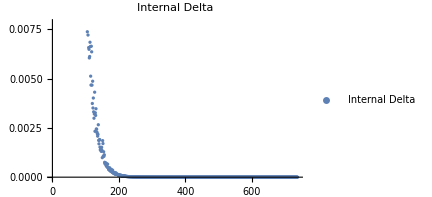
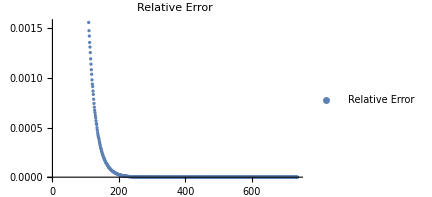
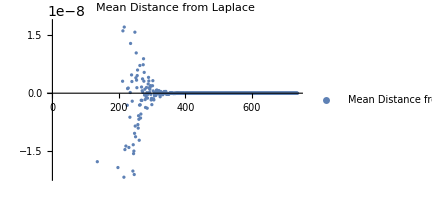
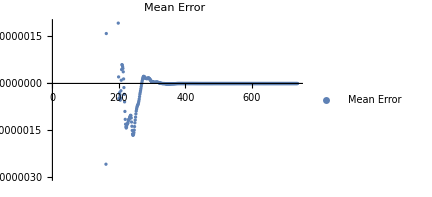
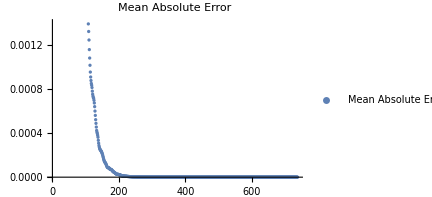
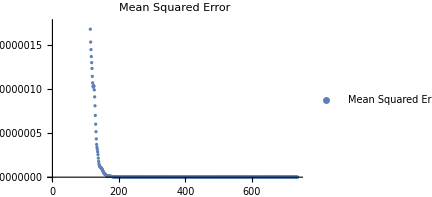
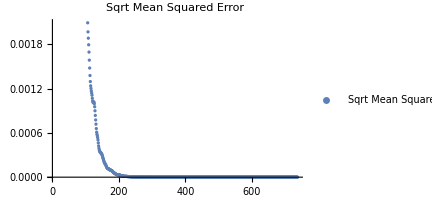

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-ConvComp-WithRelativeError-size141-tol-e-15.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Relative Error","Mean Distance from Laplace","Mean Error","Mean Absolute Error","Mean Squared Error","Sqrt Mean Squared Error"};

Row[plotsm10=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

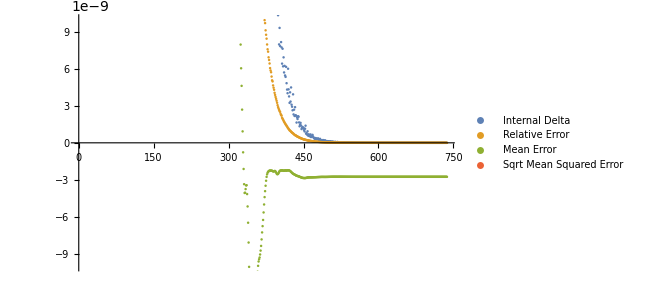

```mathematica
compareWith=5;
andWith=8;

yRange=10^(-8);

ListPlot[{
rawData[[All,{1,2}]],
rawData[[All,{1,3}]]
,rawData[[All,{1,compareWith}]]
,rawData[[All,{1,andWith}]]
},
PlotLegends->lables[[{1,2,compareWith-1,andWith-1}]],ImageSize->1.2*{400,300},PlotRange->{All,{-yRange,yRange}}
]
```

## 2dLaplaceEqSolution-ConvCompAgainst10000-WithRelativeError-size141-tol-e-15.dat

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-ConvCompAgainst10000-WithRelativeError-size141-tol-e-15.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Relative Error","Mean Distance from Laplace","Mean Error","Mean Absolute Error","Mean Squared Error","Sqrt Mean Squared Error"};

Row[plotsm10=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

{Iteration #1,Delta Internal,Error Relative,Distance from Laplace Mean,Error Mean,Absolute Error Mean,Error Mean Square,Error Mean Sqrt Square}

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

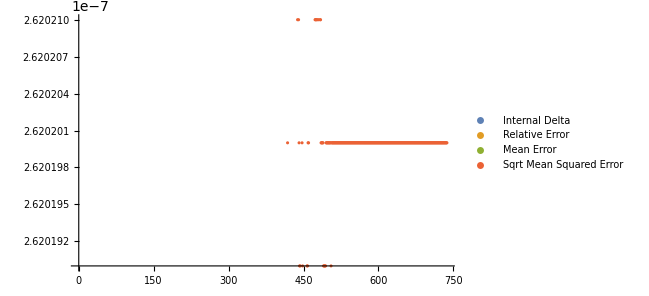

```mathematica
compareWith=5;
andWith=8;

yRange=10^(-12);

ListPlot[{
rawData[[All,{1,2}]],
rawData[[All,{1,3}]]
,rawData[[All,{1,compareWith}]]
,rawData[[All,{1,andWith}]]
},
PlotLegends->lables[[{1,2,compareWith-1,andWith-1}]],ImageSize->1.2*{400,300},PlotRange->{All,{-yRange,yRange}+2.6202*10^(-07)}
]
```

## All together

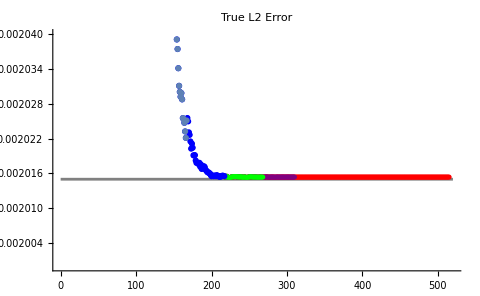
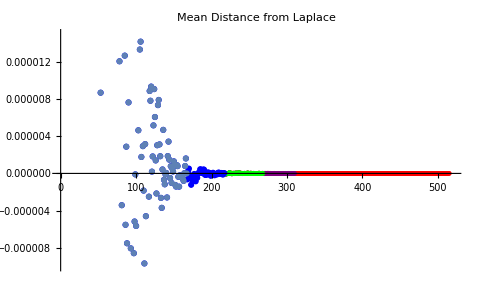

```mathematica
Row[{Show[{plots000000[[2]]/.RGBColor[___]->Red/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-7"}]},opts]
,plots000001[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
,plots000010[[2]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-5"}]},opts]
,plots000100[[2]]/.RGBColor[___]->Blue/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
,plots001000[[2]]/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-3"}]},opts],
Plot[0.002015,{x,0,520},PlotStyle->Gray]}
,ImageSize->1.2*{400,300},PlotRange->{{0,520},{0.0020,0.00204}}
]
,Show[{plots000000[[3]]/.RGBColor[___]->Red/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-7"}]},opts]
,plots000001[[3]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
,plots000010[[3]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-5"}]},opts]
,plots000100[[3]]/.RGBColor[___]->Blue/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
,plots001000[[3]]/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-3"}]},opts]
(*Plot[0.002,{x,0,520},PlotStyle->Gray]*)}
,ImageSize->1.2*{400,300},PlotRange->{{0,520},{-0.00001,0.000015}}
]
}]
```

Conclusion: 10^-5 seems the sweet spot to reach convergence!!!

# Comparison using Laplace convergence (i.e. how far from solving the laplace equation)

## L=141

### tol - e-8

{Iteration #1,Delta Internal,Distance from Laplace Mean}

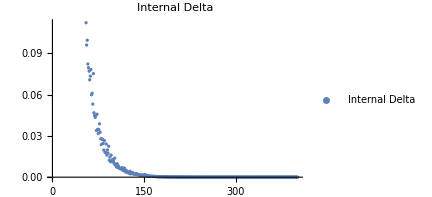
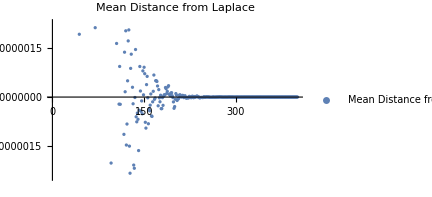

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size141-tol-e-8.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm8=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

```mathematica
rawData
```

{{1,9.33546×10^-9,1.13279×10^-11}}

#### Ansatz

```mathematica
L
```

141

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

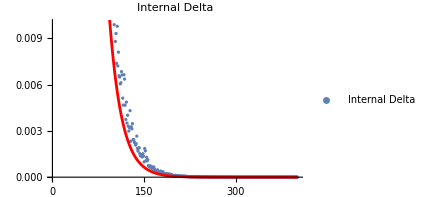

```mathematica
ϵAnsatz=Exp[-3/L Log[10]x];

endRange=Cases[plotsm8[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm8[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### tol - e-10

{Iteration #1,Delta Internal,Distance from Laplace Mean,Error L2 True,Absolute Error Mean}

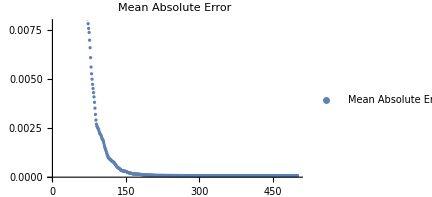
-Graphics--Graphics--Graphics--Graphics-

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size141-tol-e-10.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace","True L2 Error","Mean Absolute Error"};

Row[plotsm10=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

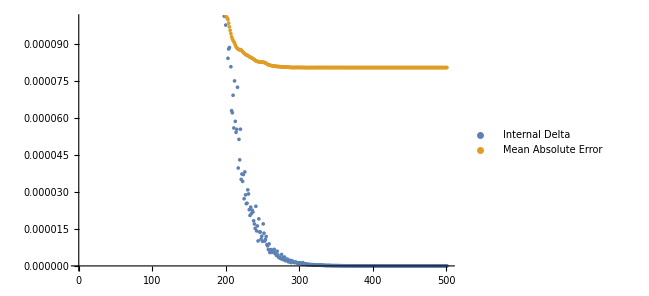

```mathematica
ListPlot[{
rawData[[All,{1,2}]],rawData[[All,{1,5}]]},
PlotLegends->lables[[{1,4}]],ImageSize->1.2*{400,300},PlotRange->{All,{0,0.0001}}
]
```

#### Ansatz for ϵ

```mathematica
L
```

161

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

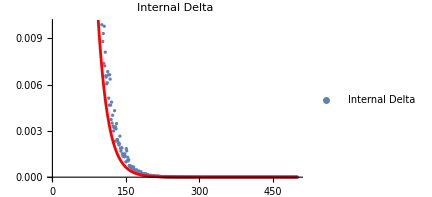

```mathematica
ϵAnsatz=Exp[-3/L Log[10]x];

endRange=Cases[plotsm10[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm10[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

#### Ansatz for Δ

```mathematica
L
```

161

```mathematica
ClearAll[ϵ,ϵAnsatz,ΔAnsatz]
```

```mathematica
data=Select[Cases[plotsm10[[2]],(Line|Point)[pts_?MatrixQ]:>pts,Infinity][[1]],#[[2]]>0&];

ΔAnsatz=ϵAnsatz *c;

FindFit[data,ΔAnsatz,c,x]

ΔAnsatz=ΔAnsatz/.%
```

{c→0.00086414}

0.00086414 10^(-x/47)

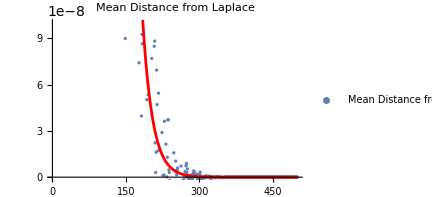

```mathematica
endRange=Cases[plotsm10[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm10[[2]]
,Plot[ΔAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.0000001}}]
```

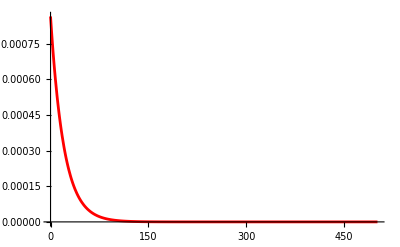

```mathematica
Plot[ΔAnsatz,{x,0,endRange},PlotStyle->Red,PlotRange->All]
```

### tol - e-12

{Iteration #1,Delta Internal,Distance from Laplace Mean,Error L2 True,Absolute Error Mean}

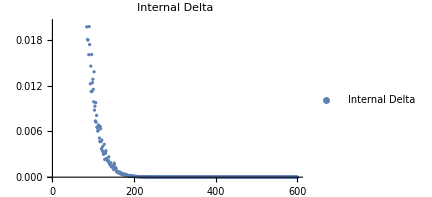
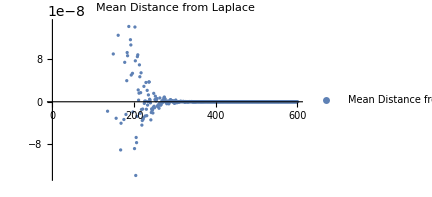
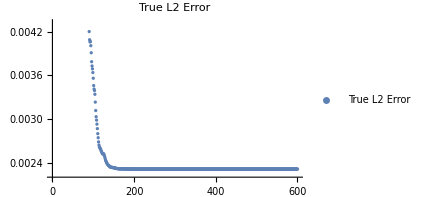
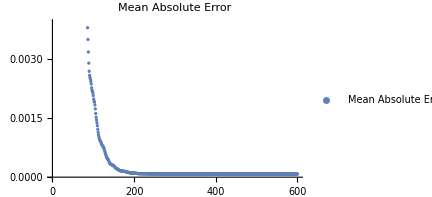

```mathematica
L=141;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size141-tol-e-12.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace","True L2 Error","Mean Absolute Error"};

Row[plotsm12=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

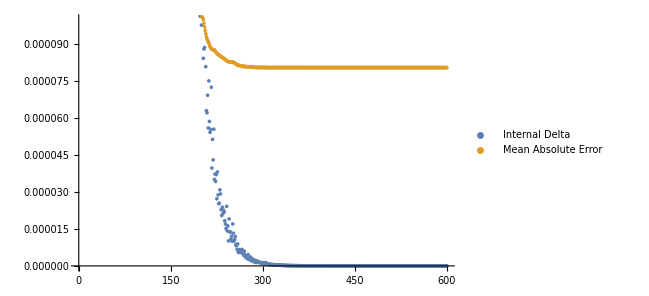

```mathematica
ListPlot[{
rawData[[All,{1,2}]],rawData[[All,{1,5}]]},
PlotLegends->lables[[{1,4}]],ImageSize->1.2*{400,300},PlotRange->{All,{0,0.0001}}
]
```

#### Ansatz for ϵ

```mathematica
L
```

161

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

```mathematica
ϵAnsatz=Exp[-3/L Log[10]x];

endRange=Cases[plotsm10[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm10[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

-Graphics-

#### Ansatz for Δ

```mathematica
L
```

161

```mathematica
ClearAll[ϵ,ϵAnsatz,ΔAnsatz]
```

```mathematica
data=Select[Cases[plotsm10[[2]],(Line|Point)[pts_?MatrixQ]:>pts,Infinity][[1]],#[[2]]>0&];

ΔAnsatz=ϵAnsatz *c;

FindFit[data,ΔAnsatz,c,x]

ΔAnsatz=ΔAnsatz/.%
```

{c→0.00086414}

0.00086414 10^(-x/47)

```mathematica
endRange=Cases[plotsm10[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm10[[2]]
,Plot[ΔAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.0000001}}]
```

-Graphics-

```mathematica
Plot[ΔAnsatz,{x,0,endRange},PlotStyle->Red,PlotRange->All]
```

-Graphics-

### All together

```mathematica
L
```

141

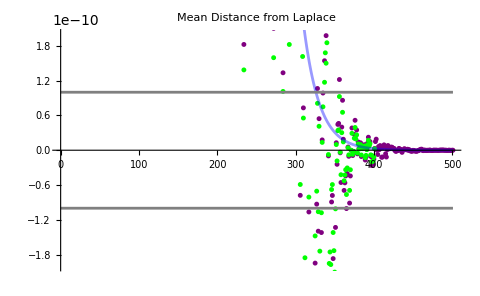

```mathematica
ϵ = 10^(-8);

range=ΔAnsatz/.x->L/3;
range=10^(-10);

endRange=Cases[plotsm10[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Row[{Show[{plotsm10[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-10"}]},opts]
,plotsm8[[2]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-8"}]},opts]
,Plot[ΔAnsatz (*Sin[0.1x]*),{x,0,endRange},PlotStyle->{RGBColor[0,0,1,0.4]}]
,Plot[range,{x,0,endRange},PlotStyle->Gray],Plot[-range,{x,0,endRange},PlotStyle->Gray]}
,ImageSize->1.2*{400,300},PlotRange->{All,{-range*2,range*2}}
]
}]
```

```mathematica
b=2.;
Table[RandomReal[{0,1}],{i,0,3}]
Total@%
(%%^b);
(Total@%)^(1/b)
```

{0.582977,0.327799,0.200432,0.616188}

1.7274

0.931222

### Scaling

#### Composite analysis:

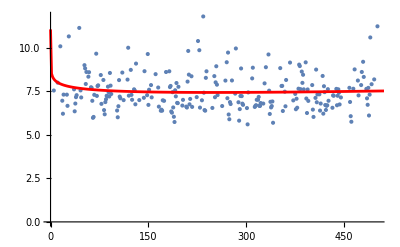

| Estimate | Standard Error | t-Statistic | P-Value
1 | 8.61579 | 0.817197 | 10.5431 | 1.02779×10^-21
x | 0.00105452 | 0.00119822 | 0.880073 | 0.379672
Log[x] | -0.263708 | 0.204829 | -1.28746 | 0.199135

```mathematica
rawData[[All,{1,2,3}]];

LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[%,#[[3]]>0&];

lm3=LinearModelFit[LinLogData,{1,x,Log[x]},x];

Show[{ListPlot[LinLogData]
,Plot[lm3[x],{x,0,5001},PlotStyle->Red]}]

lm3["ParameterTable"][[1]]//Quiet
```

{c→4194.16}

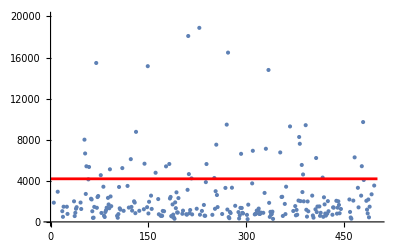

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4194.16 | 716.755 | 5.8516 | 1.52035×10^-8

```mathematica
rawData[[All,{1,2,3}]];

LinData={#[[1]],(#[[2]])/(#[[3]])}&/@Select[%,#[[3]]>0&];

endRange=LinData[[-1,1]];

FindFit[LinData,c,{c},x]
lm4=LinearModelFit[LinData,{1},x];

Show[{ListPlot[LinData]
,Plot[lm4[x],{x,0,endRange},PlotStyle->Red]
(*,Plot[c/.{c->0.0008641404073993688},{x,0,endRange},PlotStyle->Green]*)
}
,PlotRange->{All,{0,20000}}]

lm4["ParameterTable"][[1]]//Quiet
```

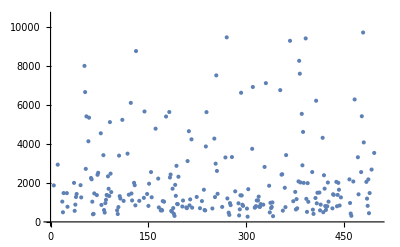

```mathematica
ListPlot[LinData]
```

```mathematica
Table[RandomReal[],{i,0,3}]
Total@%
%%^b;
(Total@%)^(1/b)
```

{0.0357346,0.983971,0.825602,0.241708}

2.08701

1.30748

## L=161

### tol - e-4

{Iteration #1,Delta Internal,Distance from Laplace Mean}

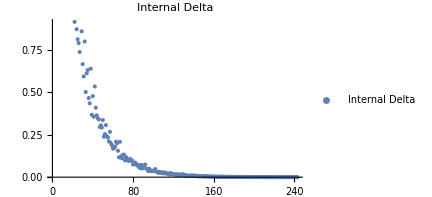
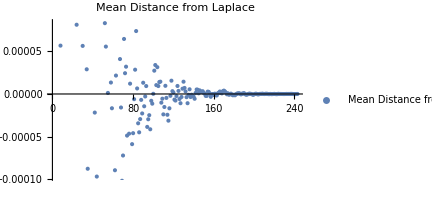

```mathematica
L=161;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size161-tol-e-4.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm4=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

#### Ansatz

```mathematica
L
```

161

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

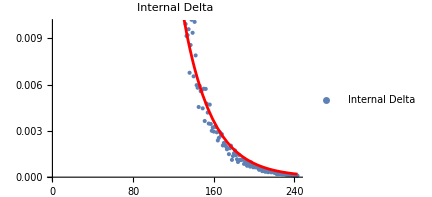

```mathematica
ϵAnsatz=Exp[-3/(L+7Log[L])Log[10]x];

endRange=Cases[plotsm4[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm4[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### All together

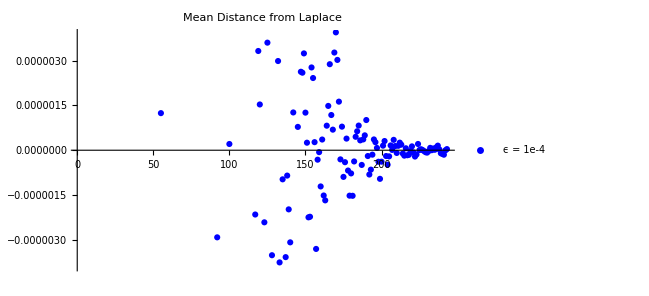

```mathematica
range=10^(-4)/161*10/1.6;

Row[{Show[{plotsm4[[2]]/.RGBColor[___]->Blue/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
(*,plots001000[[2]]/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-3"}]},opts],
Plot[0.002015,{x,0,520},PlotStyle->Gray]*)}
,ImageSize->1.2*{400,300},PlotRange->{All,{-range,range}}
]
}]
```

Conclusion: 10^-4 seems the sweet spot to reach convergence!!!

### Scaling

#### Composite analysis:

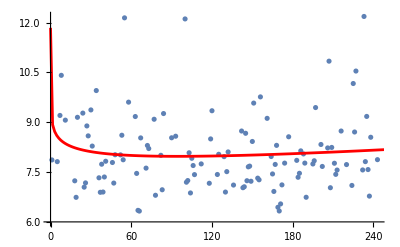

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.05335 | 0.768232 | 11.7847 | 1.02449×10^-21
x | 0.00321505 | 0.00315889 | 1.01778 | 0.310848
Log[x] | -0.303563 | 0.23926 | -1.26876 | 0.207004

```mathematica
rawData[[All,{1,2,3}]];

LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[%,#[[3]]>0&];

lm3=LinearModelFit[LinLogData,{1,x,Log[x]},x];

Show[{ListPlot[LinLogData]
,Plot[lm3[x],{x,0,5001},PlotStyle->Red]}]

lm3["ParameterTable"][[1]]//Quiet
```

## L=401

### tol - e-4

{Iteration #1,Delta Internal,Distance from Laplace Mean}

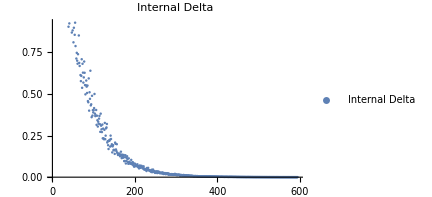
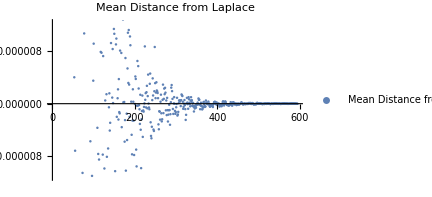

```mathematica
L=401;

rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size401-tol-e-4.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm4=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

### tol - e-5

{Iteration #1,Delta Internal,Distance from Laplace Mean}

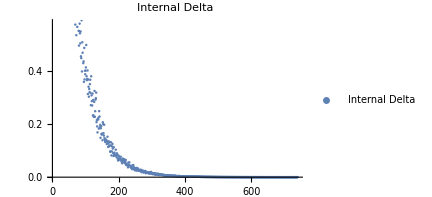
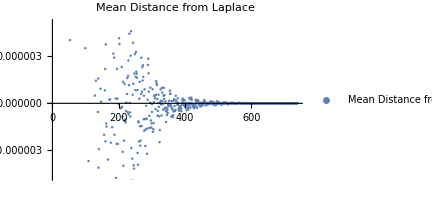

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size401-tol-e-5.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm5=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

### tol - e-6

{Iteration #1,Delta Internal,Distance from Laplace Mean}

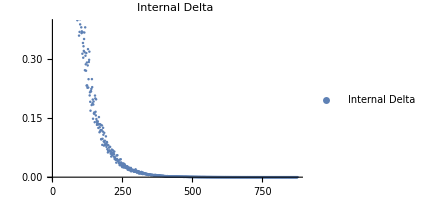
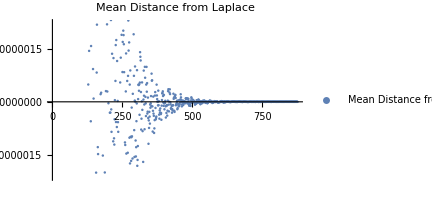

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size401-tol-e-6.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm6=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

#### Ansatz

```mathematica
L
```

401

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

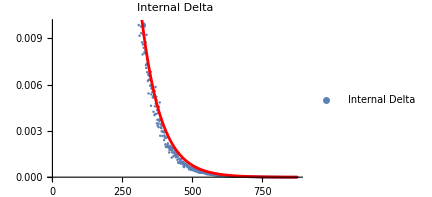

```mathematica
ϵAnsatz=Exp[-2.5/L Log[10]x];

endRange=Cases[plotsm6[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm6[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### All together

-1.24532×10^-9

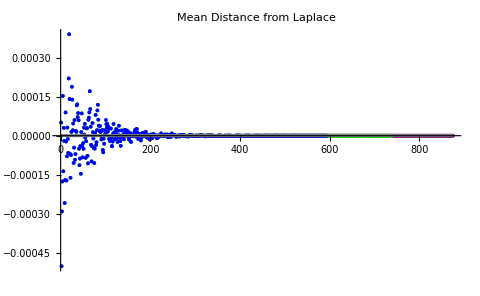

```mathematica
ϵ = 10^(-6);
L=401.;


range=ϵ/(1-(0.10*L)^2/2)

endRange=Cases[plotsm6[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Row[{Show[{plotsm6[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
,plotsm5[[2]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-5"}]},opts]
,plotsm4[[2]]/.RGBColor[___]->Blue/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
,Plot[4*10^(-6) Exp[-0.0047x]Cos[0.080x],{x,0,endRange},PlotStyle->{RGBColor[0,0,1,0.]}]
,Plot[range,{x,0,endRange},PlotStyle->Gray],Plot[-range,{x,0,endRange},PlotStyle->Gray]}
,ImageSize->1.2*{400,300},PlotRange->{All,{-range*10,range*10}}
]
}]
```

### Scaling

#### Exponential convergence: the Proxy_error goes down exponentially fast!!

```mathematica
rawData[[All,{1,2}]];
LinLogData={#[[1]],Log[#[[2]]]}&/@%;
```

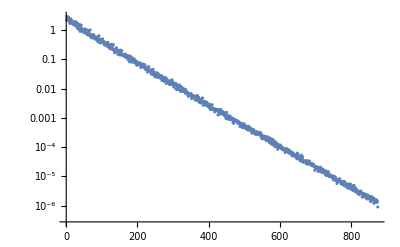

```mathematica
ListLogPlot[rawData[[All,{1,2}]]]
ListPlot[LinLogData];
```

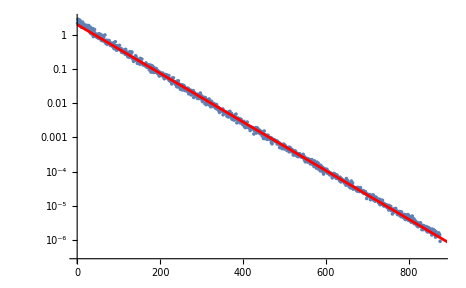

```mathematica
lm=LinearModelFit[LinLogData,x,x];

Show[{ListLogPlot[rawData[[All,{1,2}]]]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]
```

```mathematica
lm["ParameterTable"][[1]]//Quiet
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.707873 | 0.00900266 | 78.6293 | 0.
x | -0.0164233 | 0.0000178054 | -922.378 | 0.

```mathematica
3/401*Log[10.]
```

0.0172263

#### Distance from Laplacian: exponentially fast as well (but oscillating)

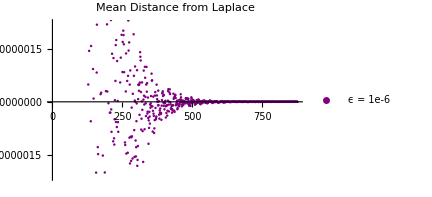

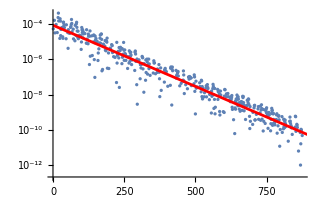

| Estimate | Standard Error | t-Statistic | P-Value
1 | -9.42359 | 0.107274 | -87.8463 | 1.53541×10^-281
x | -0.0158922 | 0.000209353 | -75.911 | 2.61829×10^-255

```mathematica
plotsm6[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
(*1. Pull the data points out of the existing plot*)
data=Cases[%,(Line|Point)[pts_?MatrixQ]:>pts,Infinity];

logdata={#[[1]],Log[#[[2]]]}&/@Select[(data[[1]]),#[[2]]>0&];


lm=LinearModelFit[logdata,x,x];

Show[{ListLogPlot[data]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]

lm["ParameterTable"][[1]]//Quiet
```

#### Composite analysis:

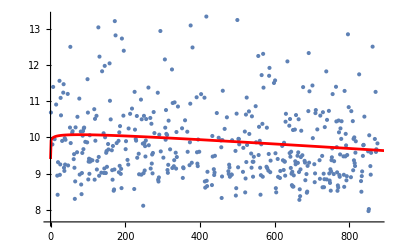

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.8974 | 0.541447 | 18.2795 | 6.02987×10^-56
x | -0.000702877 | 0.000459995 | -1.52801 | 0.127229
Log[x] | 0.0537281 | 0.122923 | 0.437088 | 0.662262

```mathematica
rawData[[All,{1,2,3}]];

LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[%,#[[3]]>0&];

lm3=LinearModelFit[LinLogData,{1,x,Log[x]},x];

Show[{ListPlot[LinLogData]
,Plot[lm3[x],{x,0,5001},PlotStyle->Red]}]

lm3["ParameterTable"][[1]]//Quiet
```

## L=1001

### tol - e-4

{Iteration #1,Delta Internal,Distance from Laplace Mean}

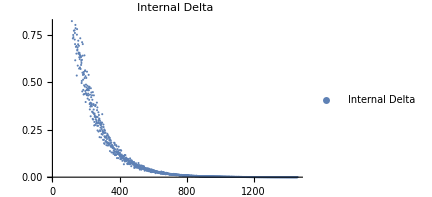
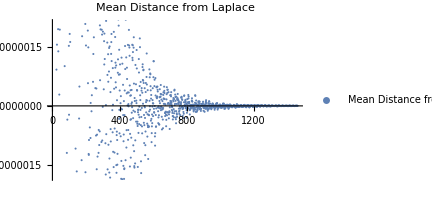

```mathematica
L=1001;
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size1001-tol-e-4.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm4=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

### tol - e-5

{Iteration #1,Delta Internal,Distance from Laplace Mean}

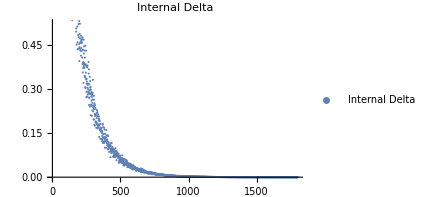
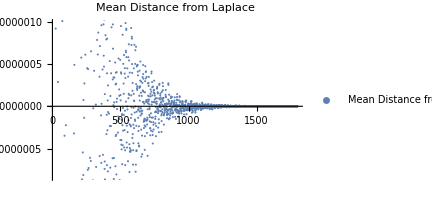

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size1001-tol-e-5.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm5=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

### tol - e-6

{Iteration #1,Delta Internal,Distance from Laplace Mean}

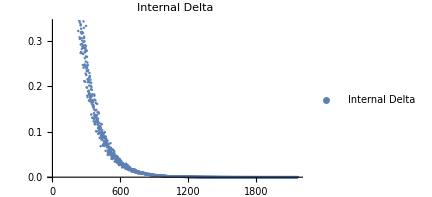
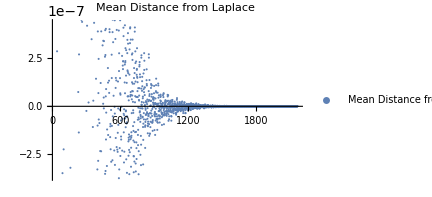

```mathematica
L=1001;
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size1001-tol-e-6.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm6=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

#### Ansatz

```mathematica
L
```

1001

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

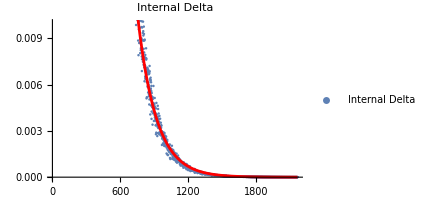

```mathematica
ϵAnsatz=Exp[-3/(L+20Log[L])Log[10]x];

endRange=Cases[plotsm6[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm6[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### All together

```mathematica
Series[Sin[x],{x,0,4}]
```

x-x^3/6+O[x]^5

3.98772×10^-6

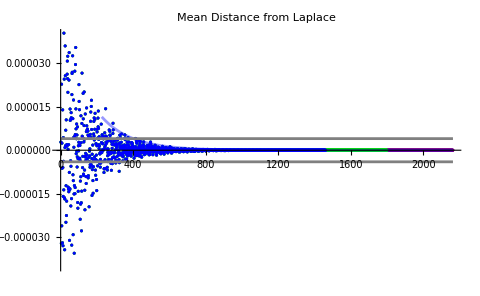

```mathematica
ϵ = 10^(-5);
L=1001.;


range=ϵAnsatz/ ((4 L)/(3Log[10]))/.x->L

endRange=Cases[plotsm6[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Row[{Show[{plotsm6[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
,plotsm5[[2]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-5"}]},opts]
,plotsm4[[2]]/.RGBColor[___]->Blue/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
,Plot[ϵAnsatz Exp[-10](*Sin[0.1x]*),{x,0,endRange},PlotStyle->{RGBColor[0,0,1,0.4]}]
,Plot[range,{x,0,endRange},PlotStyle->Gray],Plot[-range,{x,0,endRange},PlotStyle->Gray]}
,ImageSize->1.2*{400,300},PlotRange->{All,{-range*10,range*10}}
]
}]
```

### Scaling

#### Migliore says: to go from precision 10^p-> 10^(p-1) one needs L/3 more steps. TRUE!

```mathematica
n4=Cases[plotsm4[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]]
n5=Cases[plotsm5[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]]
n6=Cases[plotsm6[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]]
```

1461

1800

2164

```mathematica
n5-n4
n6-n5
1001./3
```

339

364

333.667

#### Exponential convergence: the Proxy_error goes down exponentially fast!!

```mathematica
rawData[[All,{1,2}]];
LinLogData={#[[1]],Log[#[[2]]]}&/@%;
```

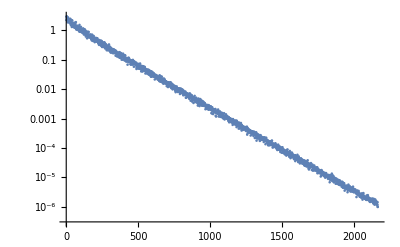

```mathematica
ListLogPlot[rawData[[All,{1,2}]]]
ListPlot[LinLogData];
```

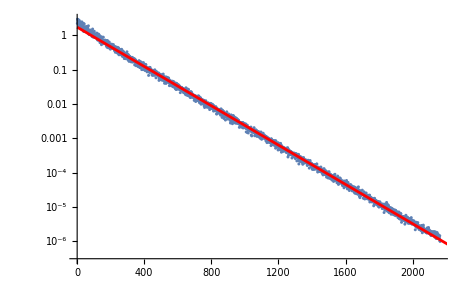

```mathematica
lm=LinearModelFit[LinLogData,x,x];

Show[{ListLogPlot[rawData[[All,{1,2}]]]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]
```

```mathematica
lm["ParameterTable"][[1]]
```

General::munfl: Exp[-1712.18] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7306.16] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.553059 | 0.00605718 | 91.3063 | 0.
x | -0.00659806 | 4.84645×10^-6 | -1361.42 | 0.

```mathematica
3/1001*Log[10.]
```

0.00690085

#### Distance from Laplacian: exponentially fast as well (but oscillating)

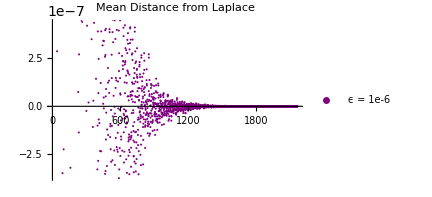

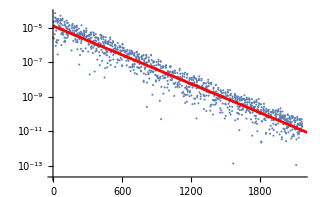

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11.2521 | 0.0648155 | -173.602 | 0.
x | -0.00645123 | 0.0000512378 | -125.908 | 0.

```mathematica
plotsm6[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
(*1. Pull the data points out of the existing plot*)
data=Cases[%,(Line|Point)[pts_?MatrixQ]:>pts,Infinity];

logdata={#[[1]],Log[#[[2]]]}&/@Select[(data[[1]]),#[[2]]>0&];


lm=LinearModelFit[logdata,x,x];

Show[{ListLogPlot[data]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]

lm["ParameterTable"][[1]]//Quiet
```

#### Composite analysis:

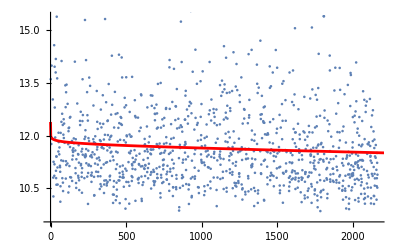

| Estimate | Standard Error | t-Statistic | P-Value
1 | 12.0111 | 0.373261 | 32.1788 | 9.23635×10^-161
x | -0.0000867697 | 0.000108523 | -0.799555 | 0.424141
Log[x] | -0.0405251 | 0.0705613 | -0.574324 | 0.565865

```mathematica
rawData[[All,{1,2,3}]];

LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[%,#[[3]]>0&];


lm3=LinearModelFit[LinLogData,{1,x,Log[x]},x];

Show[{ListPlot[LinLogData]
,Plot[lm3[x],{x,0,5001},PlotStyle->Red]}]

lm3["ParameterTable"][[1]]//Quiet
```

{c→729567.}

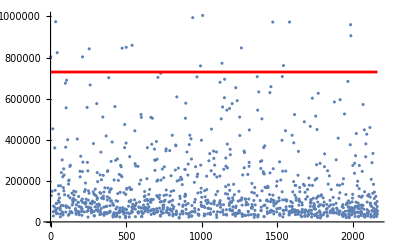

| Estimate | Standard Error | t-Statistic | P-Value
1 | 729567. | 387821. | 1.8812 | 0.060208

```mathematica
rawData[[All,{1,2,3}]];

LinData={#[[1]],(#[[2]])/(#[[3]])}&/@Select[%,#[[3]]>0&];

endRange=LinData[[-1,1]];

FindFit[LinData,c,{c},x]
lm4=LinearModelFit[LinData,{1},x];

Show[{ListPlot[LinData]
,Plot[lm4[x],{x,0,endRange},PlotStyle->Red]}
,PlotRange->{All,{0,10^6}}]

lm4["ParameterTable"][[1]]//Quiet
```

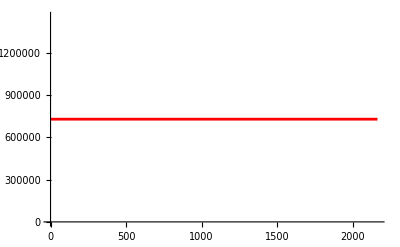

```mathematica
Plot[lm4[x],{x,0,endRange},PlotStyle->Red]
```

## L=2001

### tol - e-6

{Iteration #1,Delta Internal,Distance from Laplace Mean}

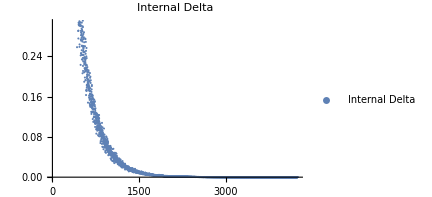
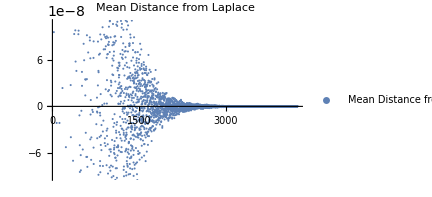

```mathematica
L=2001;
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size2001-tol-e-6.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]]
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm6=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]]
```

#### Ansatz

```mathematica
L
```

2001

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

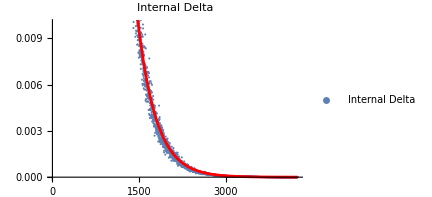

```mathematica
ϵAnsatz=Exp[-2.7/L Log[10]x];

endRange=Cases[plotsm6[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm6[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### Scaling

#### Exponential convergence: the Proxy_error goes down exponentially fast!!

```mathematica
rawData[[All,{1,2}]];
LinLogData={#[[1]],Log[#[[2]]]}&/@%;
```

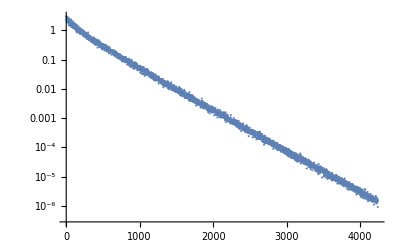

```mathematica
ListLogPlot[rawData[[All,{1,2}]]]
ListPlot[LinLogData];
```

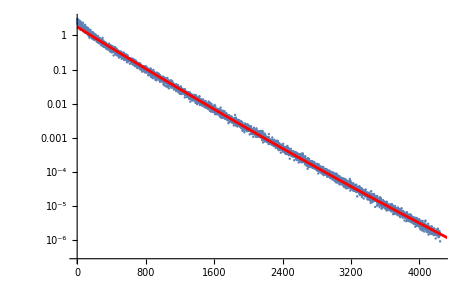

```mathematica
lm=LinearModelFit[LinLogData,{1,x,x^2},x];

Show[{ListLogPlot[rawData[[All,{1,2}]]]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]
```

```mathematica
lm["ParameterTable"][[1]]//Quiet
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.573277 | 0.00638553 | 89.7775 | 0.
x | -0.0035776 | 6.95263×10^-6 | -514.567 | 0.
x^2 | 6.69732×10^-8 | 1.58698×10^-9 | 42.2018 | 0.

#### Distance from Laplacian: exponentially fast as well (but oscillating)

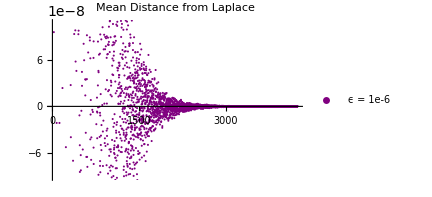

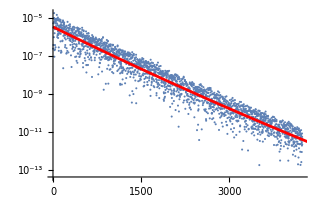

| Estimate | Standard Error | t-Statistic | P-Value
1 | -12.5401 | 0.0666957 | -188.02 | 0.
x | -0.00350314 | 0.0000737751 | -47.484 | 0.
x^2 | 6.59416×10^-8 | 1.68097×10^-8 | 3.92284 | 0.0000903029

```mathematica
plotsm6[[2]]/.RGBColor[___]->Purple/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-6"}]},opts]
(*1. Pull the data points out of the existing plot*)
data=Cases[%,(Line|Point)[pts_?MatrixQ]:>pts,Infinity];

logdata={#[[1]],Log[#[[2]]]}&/@Select[(data[[1]]),#[[2]]>0&];


lm=LinearModelFit[logdata,{1,x,x^2},x];

Show[{ListLogPlot[data]
,Plot[lm[x],{x,0,5001},PlotStyle->Red]}]

lm["ParameterTable"][[1]]//Quiet
```

#### Composite analysis:

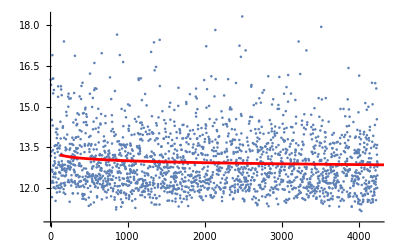

| Estimate | Standard Error | t-Statistic | P-Value
1 | 13.6802 | 0.16293 | 83.9636 | 0.
Log[(1-x^2/2)^2] | -0.0257196 | 0.00577988 | -4.44986 | 9.03881×10^-6

```mathematica
rawData[[All,{1,2,3}]];

LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[%,#[[3]]>0&];

lm3=LinearModelFit[LinLogData,{Log[(1-(x)^2/2)^2]},x];

Show[{ListPlot[LinLogData]
,Plot[lm3[x],{x,-10,5001},PlotStyle->Red]}]

lm3["ParameterTable"][[1]]//Quiet
```

## L=6001

### tol - e-4

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\convergenceData\\2dLaplaceEqSolution-conv-size6001-tol-e-4.dat"}],"CSV"]; (* MODIFY FILE NAME *)
(*rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];*)
rawData[[1]];
rawData = Delete[rawData,1];

numCols=Last[Dimensions[rawData]];
lables={"Internal Delta","Mean Distance from Laplace"};

Row[plotsm4=Table[
ListPlot[rawData[[All,{1,i}]],
PlotLabel->lables[[i-1]],PlotLegends->Placed[{lables[[i-1]]},{Right,Top}],ImageSize->.8*{400,300}],{i,2,numCols}]];
```

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

1800.6

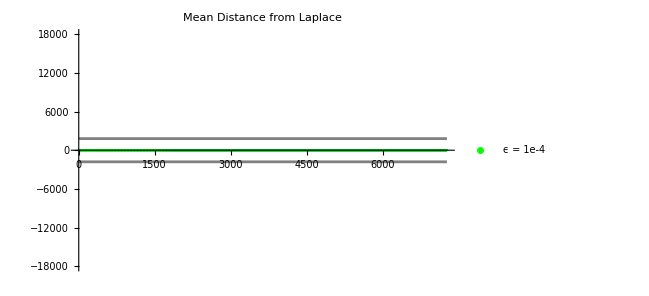

```mathematica
ϵ = 10^(-4);
L=6001.;


range=ϵ/(1-L^2/2);

range=ϵ(1+(L)^2/2)

endRange=Cases[plotsm4[[2]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Row[{Show[{plotsm4[[2]]/.RGBColor[___]->Green/.PointLegend[bef_,{__},opts__]:>PointLegend[bef,{Row[{"ϵ = 1e-4"}]},opts]
,Plot[range,{x,0,endRange},PlotStyle->Gray],Plot[-range,{x,0,endRange},PlotStyle->Gray]
,Plot[10^(-6) Exp[-0.001x]Cos[0.050x],{x,0,endRange},PlotStyle->{RGBColor[0,0,1,0.2]}]
}
,ImageSize->1.2*{400,300},PlotRange->{All,{-range*10,range*10}}
]
}]
```

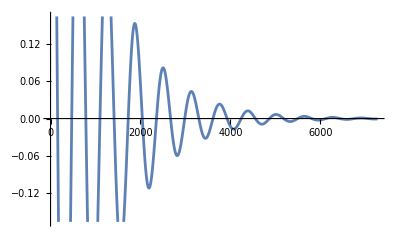

```mathematica
Plot[Exp[-0.0010x]Cos[0.010x],{x,0,endRange}]
```

#### Ansatz

```mathematica
L
```

6001.

```mathematica
ClearAll[ϵ,ϵAnsatz]
```

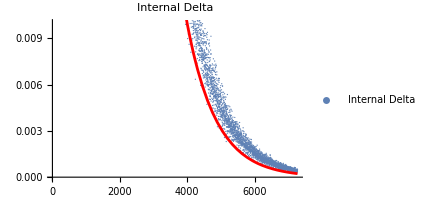

```mathematica
ϵAnsatz=Exp[-3/(L+Log[L])Log[10]x];

endRange=Cases[plotsm4[[1]],Point[pts_?MatrixQ]:>Length[pts],Infinity][[1]];

Show[{plotsm4[[1]]
,Plot[ϵAnsatz,{x,0,endRange},PlotStyle->Red]
}
,PlotRange->{{0,endRange},{0,0.01}}]
```

### Scaling

#### Composite analysis:

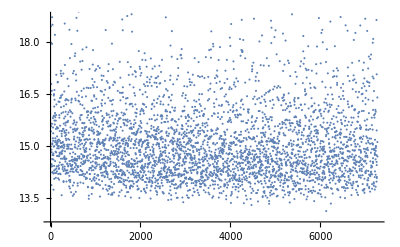

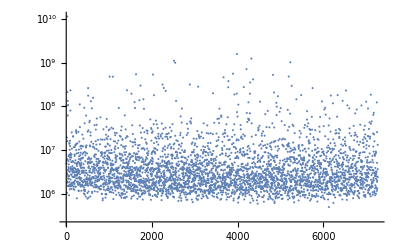

```mathematica
ListPlot[LinLogData]
ListLogPlot[Data]
```

```mathematica
LinLogData={#[[1]],Log[#[[2]]]-Log[#[[3]]]}&/@Select[rawData[[All,{1,2,3}]],#[[3]]>0&];

Data={#[[1]],#[[2]]/#[[3]]}&/@Select[rawData[[All,{1,2,3}]],#[[3]]>0&];

lm3=LinearModelFit[LinLogData,{Log[(1-(x)^2/2)^2]},x];

Show[{(*ListPlot[LinLogData]
,*)ListLogPlot[Data]
,Plot[lm3[x],{x,0,8001},PlotStyle->Red]
(*,Plot[-1.56+Log[x^2],{x,0,8001},PlotStyle->Green]*)}]

lm3["ParameterTable"][[1]]//Quiet
```

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | 15.6594 | 0.142711 | 109.729 | 0.
Log[(1-x^2/2)^2] | -0.0188453 | 0.00470084 | -4.00892 | 0.0000621841

```mathematica
Series[1/Cos[x],{x,0,4}]
```

1+x^2/2+(5 x^4)/24+O[x]^5

## From the sacling of all the data: ϵ/Δ ~ Exp[-const ] but there still is an L dependence (very likely a Log correction): Log[Cos[x]^2] ~ Log[(1 - (x)^2/2)^2]

```mathematica
Series[Cos[x],{x,0,2}]
```

1-x^2/2+O[x]^3

```mathematica
fitFunc=c+b*Log[(1-(x)^2/2)^2];
fitSol=FindFit[data,fitFunc,{b,c},x]



Show[{ListPlot[data]
,Plot[fitFunc/.fitSol,{x,100,7000}]}]
```

{b→0.481977,c→-0.893568}

-Graphics-

```mathematica
fitFunc/.fitSol
```

12.8053+1.22606 Log[Cos[0.999957 x]^2]

```mathematica
data={{161,8.11},{401,10.13},{1001,11.80},{2001,13.10},{6001,15.15}};

lmLog= LinearModelFit[data,{1,Log[x]},x];
lmLogCos= LinearModelFit[data,{1,Log[(1-x^2/2)^2]},x];


Show[{ListPlot[data]
,Plot[lmLog[x],{x,100,7000}]
,Plot[lmLogCos[x],{x,100,7000},PlotStyle->{Dashed,Green}]
}]

Quiet@lmLog["ParameterTable"][[1]]
Quiet@lmLogCos["ParameterTable"][[1]]
```

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.56187 | 0.285584 | -5.46903 | 0.0120168
Log[x] | 1.92793 | 0.0409699 | 47.0571 | 0.0000211295

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.893568 | 0.271574 | -3.29033 | 0.0460664
Log[(1-x^2/2)^2] | 0.481977 | 0.0102404 | 47.0661 | 0.0000211174

# “Experiment”

## No source

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\SOR-convergence-scaling.csv"}],"CSV"]; (* MODIFY FILE NAME *)
rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];
ListPlot[rawData]
ListLogLogPlot[rawData]
```

-Graphics-

-Graphics-

```mathematica
rawData1=Select[rawData,#[[1]]<=133&];
rawData2=Select[rawData,#[[1]]>133&];
```

```mathematica
ListPlot[rawData1]
ListLogLogPlot[rawData1]

ListPlot[rawData2]
ListLogLogPlot[rawData2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
FindFit[Log[rawData1],a+df *x,{a,df},x]
FindFit[Log[rawData2],a+df *x,{a,df},x]
```

{a→0.712934,df→0.983299}

{a→-3.71988,df→1.90794}

```mathematica
{{lm1=LinearModelFit[Log[rawData1],x,x];}, {lm2=LinearModelFit[Log[rawData2],x,x];}}
```

{{Null},{Null}}

```mathematica
lm["ParameterErrors"]
```

{0.00785348,0.00149191}

```mathematica
Show[ListLogLogPlot[rawData1],
Plot[lm1[x],{x,0,1000},PlotStyle->Red]
(*,PlotLabel->Row[{" b = ",b}]*)]

Print[ "d_f=",df/.FindFit[Log[rawData1],a+df *x,{a,df},x],"±",lm1["ParameterErrors"][[2]]]

Show[ListLogLogPlot[rawData2],
Plot[lm2[x],{x,0,1000},PlotStyle->Red]
(*,PlotLabel->Row[{" b = ",b}]*)]

Print[ "d_f=",df/.FindFit[Log[rawData2],a+df *x,{a,df},x],"±",lm1["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.983299±0.00362337

-Graphics-

d_f=1.90794±0.00362337

### Drop the first few

```mathematica
threshold=120;
dropped=dropped1=DeleteCases[rawData1,{a_,_}/;a>threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData1,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,0,Log[threshold-1]},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.991415±0.00240659

```mathematica
threshold=130;
dropped=dropped2=DeleteCases[rawData2,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData2,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],500},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=1.83057±0.00574361

## Central source

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\SOR-convergence-scaling-CentralSource.csv"}],"CSV"]; (* MODIFY FILE NAME *)
rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];
ListPlot[rawData]
ListLogLogPlot[rawData]
```

-Graphics-

-Graphics-

```mathematica
rawData1=Select[rawData,#[[1]]<=133&];
rawData2=Select[rawData,#[[1]]>133&];
```

```mathematica
ListPlot[rawData1]
ListLogLogPlot[rawData1]

ListPlot[rawData2]
ListLogLogPlot[rawData2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Drop the first few

```mathematica
threshold=125;
dropped=dropped1=DeleteCases[rawData1,{a_,_}/;a>threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData1,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,0,Log[threshold-1]},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.936435±0.00258789

```mathematica
threshold=130;
dropped=dropped2=DeleteCases[rawData2,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData2,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],500},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=1.6316±0.00662331

## Central source kaysProposal

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\SOR-convergence-scaling-CentralSource-kaysProposal.csv"}],"CSV"]; (* MODIFY FILE NAME *)
rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];
ListPlot[rawData]
ListLogLogPlot[rawData]
```

-Graphics-

-Graphics-

```mathematica
rawData1=Select[rawData,#[[1]]<=123&];
rawData2=Select[rawData,#[[1]]>123&];
ListPlot[rawData1]
ListLogLogPlot[rawData1]

ListPlot[rawData2]
ListLogLogPlot[rawData2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Drop the first few

```mathematica
threshold=125;
dropped=dropped1=DeleteCases[rawData1,{a_,_}/;a>threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData1,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,0,Log[threshold-1]},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=1.90084±0.00595806

```mathematica
threshold=130;
dropped=dropped2=DeleteCases[rawData2,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData2,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],500},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.950074±0.00189491

## Central source kaysProposal2

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\SOR-convergence-scaling-CentralSource-kaysProposal2.csv"}],"CSV"]; (* MODIFY FILE NAME *)
rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];
ListPlot[rawData]
ListLogLogPlot[rawData]
```

-Graphics-

-Graphics-

```mathematica
rawData1=Select[rawData,#[[1]]<=123&];
rawData2=Select[rawData,#[[1]]>123&];
ListPlot[rawData1]
ListLogLogPlot[rawData1]

ListPlot[rawData2]
ListLogLogPlot[rawData2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Drop the first few

```mathematica
threshold=125;
dropped=dropped1=DeleteCases[rawData1,{a_,_}/;a>threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData1,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,0,Log[threshold-1]},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=1.82036±0.004815

```mathematica
threshold=130;
dropped=dropped2=DeleteCases[rawData2,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData2,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],500},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.950074±0.00189491

## Central source kaysProposal5

```mathematica
rawData=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\SOR-convergence-scaling-CentralSource-kaysProposal5.csv"}],"CSV"]; (* MODIFY FILE NAME *)
rawData=DeleteDuplicates[Select[rawData,NumericQ[#[[1]]]&]];
ListPlot[rawData]
ListLogLogPlot[rawData]
```

-Graphics-

-Graphics-

```mathematica
rawData1=Select[rawData,#[[1]]<=123&];
rawData2=Select[rawData,#[[1]]>123&];
ListPlot[rawData1]
ListLogLogPlot[rawData1]

ListPlot[rawData2]
ListLogLogPlot[rawData2]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Drop the first few

```mathematica
threshold=125;
dropped=dropped1=DeleteCases[rawData1,{a_,_}/;a>threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData1,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,0,Log[threshold-1]},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=1.64743±0.0108854

```mathematica
threshold=130;
dropped=dropped2=DeleteCases[rawData2,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData2,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],500},PlotStyle->Red]}
(*PlotRange->All,*)]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]]]
```

-Graphics-

d_f=0.950074±0.00189491

StringForm::sfr: Item 2 requested in "Value `1` returned from `2` was not an integer." out of range; 1 items available.

Internal`CreateAsynchronousTask::id: Value LibraryFunctionError[LIBRARY_FUNCTION_ERROR, 6] returned from `2` was not an integer.

StringForm::sfr: Item 2 requested in "Value `1` returned from `2` was not an integer." out of range; 1 items available.

Internal`CreateAsynchronousTask::id: Value LibraryFunctionError[LIBRARY_FUNCTION_ERROR, 6] returned from `2` was not an integer.

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the
    Wolfram cloud.